```mathematica
<<NeuralNetworks`
```

```mathematica
resource=ResourceObject["MNIST"];trainingData=ResourceData[resource,"TrainingData"];testData=ResourceData[resource,"TestData"];
```

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→5,-Graphics-→6,-Graphics-→8,-Graphics-→9,-Graphics-→1}

```mathematica
lenet=NetChain[{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,10,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",Range[0,9]}],"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]]
```

NetChain[]

```mathematica
lenet=NetTrain[lenet,trainingData,ValidationSet->testData,MaxTrainingRounds->3];
```

```mathematica
NetExtract[lenet,{All,"Weights"}]
```

Failure[…]

```mathematica
NetExtract[lenet[[1]],"Weights"]
```

Part::partd: Part specification … is longer than depth of object.

NetExtract[(NetChain[])⟦1⟧,Weights]

```mathematica
imgs=Keys@RandomSample[testData,5];Thread[imgs->lenet[imgs]]
```

{-Graphics-→8,-Graphics-→9,-Graphics-→7,-Graphics-→5,-Graphics-→0}

```mathematica
TraditionalForm[lenet]
```

NetChain[<|Type→Chain,Layers→<|1→<|Type→Convolution,Arrays→<|Weights→RawArray[Real32,<20,1,5,5>],Biases→RawArray[Real32,<20>]|>,Parameters→<|OutputChannels→20,KernelSize→{5,5},Stride→{1,1},PaddingSize→{0,0},Dilation→{1,1},InputChannels→1,$GroupNumber→1,$InputSize→{28,28},$OutputSize→{24,24}|>,Inputs→<|Input→ChannelT(1,TensorT(2,{28,28}))|>,Outputs→<|Output→ChannelT(20,TensorT(2,{24,24}))|>|>,2→<|Type→Elementwise,Arrays→<||>,Parameters→<|Function→Ramp,$Dimensions→{20,24,24},$Rank→3|>,Inputs→<|Input→ChannelT(20,TensorT(2,{24,24}))|>,Outputs→<|Output→TensorT(3,{20,24,24})|>|>,3→<|Type→Pooling,Arrays→<||>,Parameters→<|KernelSize→{2,2},Stride→{2,2},PaddingSize→{0,0},Function→Max,Channels→20,$InputSize→{24,24},$OutputSize→{12,12}|>,Inputs→<|Input→TensorT(3,{20,24,24})|>,Outputs→<|Output→ChannelT(20,TensorT(2,{12,12}))|>|>,4→<|Type→Convolution,Arrays→<|Weights→RawArray[Real32,<50,20,5,5>],Biases→RawArray[Real32,<50>]|>,Parameters→<|OutputChannels→50,KernelSize→{5,5},Stride→{1,1},PaddingSize→{0,0},Dilation→{1,1},InputChannels→20,$GroupNumber→1,$InputSize→{12,12},$OutputSize→{8,8}|>,Inputs→<|Input→ChannelT(20,TensorT(2,{12,12}))|>,Outputs→<|Output→ChannelT(50,TensorT(2,{8,8}))|>|>,5→<|Type→Elementwise,Arrays→<||>,Parameters→<|Function→Ramp,$Dimensions→{50,8,8},$Rank→3|>,Inputs→<|Input→ChannelT(50,TensorT(2,{8,8}))|>,Outputs→<|Output→TensorT(3,{50,8,8})|>|>,6→<|Type→Pooling,Arrays→<||>,Parameters→<|KernelSize→{2,2},Stride→{2,2},PaddingSize→{0,0},Function→Max,Channels→50,$InputSize→{8,8},$OutputSize→{4,4}|>,Inputs→<|Input→TensorT(3,{50,8,8})|>,Outputs→<|Output→ChannelT(50,TensorT(2,{4,4}))|>|>,7→<|Type→Flatten,Arrays→<||>,Parameters→<|Dimensions→{50,4,4},$Rank→3,$OutputSize→800|>,Inputs→<|Input→ChannelT(50,TensorT(2,{4,4}))|>,Outputs→<|Output→TensorT(1,{800})|>|>,8→<|Type→DotPlus,Arrays→<|Weights→RawArray[Real32,<500,800>],Biases→RawArray[Real32,<500>]|>,Parameters→<|Size→500,$InputSize→800|>,Inputs→<|Input→TensorT(1,{800})|>,Outputs→<|Output→TensorT(1,{500})|>|>,9→<|Type→Elementwise,Arrays→<||>,Parameters→<|Function→Ramp,$Dimensions→{500},$Rank→1|>,Inputs→<|Input→TensorT(1,{500})|>,Outputs→<|Output→TensorT(1,{500})|>|>,10→<|Type→DotPlus,Arrays→<|Weights→RawArray[Real32,<10,500>],Biases→RawArray[Real32,<10>]|>,Parameters→<|Size→10,$InputSize→500|>,Inputs→<|Input→TensorT(1,{500})|>,Outputs→<|Output→TensorT(1,{10})|>|>,11→<|Type→Softmax,Arrays→<||>,Parameters→<|Size→10|>,Inputs→<|Input→TensorT(1,{10})|>,Outputs→<|Output→TensorT(1,{10})|>|>|>,Connections→{NetPort[Layers,1,Inputs,Input]→NetPort[Inputs,Input],NetPort[Layers,2,Inputs,Input]→NetPort[Layers,1,Outputs,Output],NetPort[Layers,3,Inputs,Input]→NetPort[Layers,2,Outputs,Output],NetPort[Layers,4,Inputs,Input]→NetPort[Layers,3,Outputs,Output],NetPort[Layers,5,Inputs,Input]→NetPort[Layers,4,Outputs,Output],NetPort[Layers,6,Inputs,Input]→NetPort[Layers,5,Outputs,Output],NetPort[Layers,7,Inputs,Input]→NetPort[Layers,6,Outputs,Output],NetPort[Layers,8,Inputs,Input]→NetPort[Layers,7,Outputs,Output],NetPort[Layers,9,Inputs,Input]→NetPort[Layers,8,Outputs,Output],NetPort[Layers,10,Inputs,Input]→NetPort[Layers,9,Outputs,Output],NetPort[Layers,11,Inputs,Input]→NetPort[Layers,10,Outputs,Output],NetPort[Outputs,Output]→NetPort[Layers,11,Outputs,Output]},Inputs→<|Input→EncodedType(NetEncoder[Image,<|Parameters→<|ImageSize→{28,28},ColorSpace→Grayscale,ColorChannels→1,$AugmentationFunction→None,Parallelize→False,MeanImage→None|>,Output→ChannelT(1,TensorT(2,{28,28}))|>],ChannelT(1,TensorT(2,{28,28})))|>,Outputs→<|Output→DecodedType(NetDecoder[Class,<|Parameters→<|Labels→{0,1,2,3,4,5,6,7,8,9},Dimensions→10|>,Input→TensorT(1,{10})|>],TensorT(1,{10}))|>|>]

```mathematica
OwnValues[lenet]
```

{HoldPattern[lenet]:>NetChain[]}

```mathematica
NetExtract[lenet,{ConvolutionLayer[1],"Weights"}]
```

Failure[…]

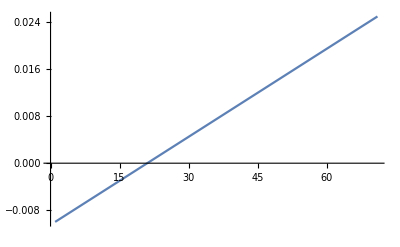

Failure[…]

```mathematica
batchNet=NetInitialize[BatchNormalizationLayer["Input"->{1}]];

ListLinePlot[Flatten[Table[{i-batchNet[{i}]},{i,-20,50}]]]

tensor334={{{1,2,10,20},{3,4,30,40},{5,6,50,60}},{{5,6,50,60},{7,8,70,80},{9,10,90,100}},{{1000,10000,1,5},{500,5000,12,215},{21312,325,6234,412}}};

batchNet=NetInitialize[BatchNormalizationLayer["Input"->{3,3,4}]];

batchNet[tensor]
```

```mathematica
a={{{1},{2},{3}}};
a//Dimensions
b=CatenateLayer[][a]
b//Dimensions
c=CatenateLayer[][b]
c//Dimensions
```

{1,3,1}

{{1},{2},{3}}

{3,1}

{1,2,3}

{3}